-Graphics-

```mathematica
pi[3]=Style["b",FontSize->18,FontFamily->"Chess Cases",FontSlant->Plain,FontColor->Red];
pi[5]=Style["n",FontSize->18,FontFamily->"Chess Cases",FontSlant->Plain,FontColor->Green];
pi[1]=Style["r",FontSize->18,FontFamily->"Chess Cases",FontSlant->Plain,FontColor->Blue];
pi[2]=Style["k",FontSize->18,FontFamily->"Chess Cases",FontSlant->Plain];
pi[4]=Style["q",FontSize->18,FontFamily->"Chess Cases",FontSlant->Plain,FontColor->Orange];
```

```mathematica
neigh1[p_]:=Map[p+#&,{{0,1},{0,-1},{1,0},{-1,0}}]
```

```mathematica
neigh2[p_]:=Map[p+#&,{{1,1},{1,-1},{-1,-1},{-1,1}}]
```

```mathematica
width=8;
solns={};
stac={{{1,1},{1,2}},{{1,1},{2,1}}};
While[Length[stac]>0,
cur=First[stac];
stac=Rest[stac];
pos=Last[cur];
If[pos=={width,width},AppendTo[solns,cur]];
next=Select[neigh1[pos],1≤#[[1]]≤width&&1≤#[[2]]≤width&&Not[MemberQ[cur,#]]&];
next=Select[next,neigh1[#]~Intersection~cur=={pos}&&MemberQ[{{},{cur[[-2]]}},neigh2[#]~Intersection~cur]&];
stac=Join[Map[cur~Join~{#}&,next],stac]
];
```

```mathematica
Length[solns] (* width=3 *)
```

6

```mathematica
Length[solns] (* width=4 *)
```

20

```mathematica
Length[solns] (* width=5 *)
```

90

```mathematica
Length[solns] (* width=6 *)
```

696

```mathematica
Length[solns] (* width=7 *)
```

12996

```mathematica
Length[solns] (* width=8 *)
```

550444

```mathematica
beforepic[r_]:=Style[Graphics[{Map[Text[pi[#[[1]]],#[[2]]-{1/2,.65-If[1<#[[1]]<5,.04,0]}]&,r],Black,Table[Line[{{0,i},{width,i}}],{i,0,width}],Table[Line[{{i,0},{i,width}}],{i,0,width}]},ImageSize->20width],Antialiasing->False]
```

```mathematica
afterpic[L_,r_]:=Style[Graphics[{Map[Text[pi[#[[1]]],#[[2]]-{1/2,.65-If[1<#[[1]]<5,.04,0]}]&,r],GrayLevel[.7],Map[Rectangle[#-1,#]&,L],Black,Table[Line[{{0,i},{width,i}}],{i,0,width}],Table[Line[{{i,0},{i,width}}],{i,0,width}]},ImageSize->20width],Antialiasing->False]
```

```mathematica
king[L_,pos_]:=Length[Intersection[neigh1[pos]~Union~neigh2[pos],L]]
```

```mathematica
ct[L_,pos_,dir_]:=Module[{c=0,p=pos+dir},
While[1≤p[[1]]≤width&&1≤p[[2]]≤width&&Not[MemberQ[Transpose[allpieces][[2]],p]],If[MemberQ[L,p],c++];p=p+dir];c]
```

```mathematica
rook[L_,pos_]:=Length[Select[L,#[[1]]==pos[[1]]||#[[2]]==pos[[2]]&]]
```

```mathematica
rook[L_,pos_]:=Total[Map[ct[L,pos,#]&,neigh1[{0,0}]]]
```

```mathematica
bishop[L_,pos_]:=Length[Select[L,Abs[#[[1]]-pos[[1]]]==Abs[#[[2]]-pos[[2]]]&]]
```

```mathematica
bishop[L_,pos_]:=Total[Map[ct[L,pos,#]&,neigh2[{0,0}]]]
```

```mathematica
queen[L_,pos_]:=rook[L,pos]+bishop[L,pos]
```

```mathematica
knight[L_,pos_]:=Length[Intersection[Map[pos+#&,{{1,2},{2,1},{1,-2},{-2,1},{2,-1},{-1,2},{-1,-2},{-2,-1}}],L]]
```

```mathematica
piece[n_]:={rook,king,bishop,queen,knight}[[n]]
```

```mathematica
numbers[L_,sn_]:=Map[piece[#[[1]]][sn,#[[2]]]&,L]
```

```mathematica
restrict[L_]:=Select[solns,Length[Union[numbers[L,#]]]==1&& Intersection[#,Transpose[L][[2]]]=={}&]
```

```mathematica
For[n=1,n>0,n++,
{p1,p2,p3,p4,p5}=Range[5];
i1=RandomInteger[{1,width}];
j1=RandomInteger[{1,width}];
i2=RandomInteger[{1,width}];
j2=RandomInteger[{1,width}];
i3=RandomInteger[{1,width}];
j3=RandomInteger[{1,width}];
i4=RandomInteger[{1,width}];
j4=RandomInteger[{1,width}];
i5=RandomInteger[{1,width}];
j5=RandomInteger[{1,width}];
allpieces={{p1,{i1,j1}},{p2,{i2,j2}},{p3,{i3,j3}},{p4,{i4,j4}},{p5,{i5,j5}}};
w=restrict[allpieces];Print[Length[w]];
If[Length[w]==1,Print[beforepic[allpieces]];Print[afterpic[w[[1]],allpieces]]]]
```

```mathematica
sss=Select[solns,Length[#]>30&];
```

```mathematica
Length[sss]
```

355220

```mathematica
For[k=1,k>0,k++,single=sss[[RandomInteger[{1,Length[sss]}]]];
{p1,p2,p3,p4,p5}=Range[5];
i1=RandomInteger[{1,width}];
j1=RandomInteger[{1,width}];
i2=RandomInteger[{1,width}];
j2=RandomInteger[{1,width}];
i3=RandomInteger[{1,width}];
j3=RandomInteger[{1,width}];
i4=RandomInteger[{1,width}];
j4=RandomInteger[{1,width}];
i5=RandomInteger[{1,width}];
j5=RandomInteger[{1,width}];
allpieces={{p1,{i1,j1}},{p2,{i2,j2}},{p3,{i3,j3}},{p4,{i4,j4}},{p5,{i5,j5}}};
If[Length[Union[numbers[allpieces,single]]]==1&& Intersection[single,Transpose[allpieces][[2]]]=={},
w=restrict[allpieces];Print[Length[w]];
If[Length[w]==1,Print[beforepic[allpieces]];Print[afterpic[w[[1]],allpieces]]]]]
```

## 6x6 3 pieces

-Graphics-

-Graphics-

-Graphics-

«265 more identical outputs»

$Aborted

## 7x7 3 pieces

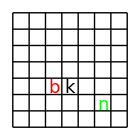

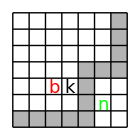

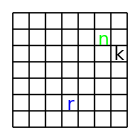

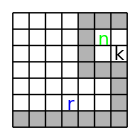

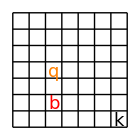

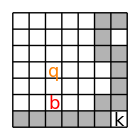

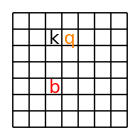

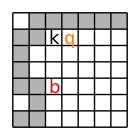

## 7x7 4 pieces

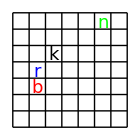

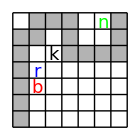

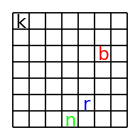

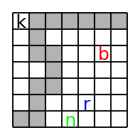

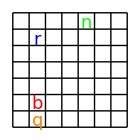

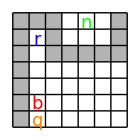

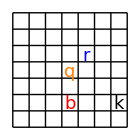

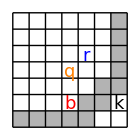

-Graphics-

-Graphics-

-Graphics-

«29 more identical outputs»

## 8x8 4 pieces

-Graphics-

-Graphics-

## 8x8 5 pieces

-Graphics-

-Graphics-

-Graphics-

«69 more identical outputs»